Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 3

Metoda Adamsa-Moultona

Napisać procedurę realizującą algorytm czterokrokowej metody Adamsa-Moultona (argumenty:  f, x_0, y_0, b, n, m).
Wykorzystać metodę iteracji prostej  (m powtórzeń), a jako metodę startową zastosować metodę Rungego-Kutty rzędy czwartego. Zminimalizować liczbę obliczeń funkcji   f.


Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=sin y(x),  x∈[0,25],
y(0)=1.

Obliczenia wykonać dla 10 i 20 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

```mathematica
(* Badana funkcja *)
func[x_,y_]:=Sin[y];
```

```mathematica
(* Metoda Rungego-Kutty rzędu czwartego *)
mrk4[f_,x0_,y0_,h_,n_]:=Module[{x,y,results},
x = x0;
y = y0;
results = {{x,y}};
Do[
k1 = f[x,y];
k2 =f[x+1/2 h, y +1/2 h*k1];
k3 = f[x+1/2 h,y+1/2 h*k2];
k4 = f[x+h, y+h*k3];
x = x + h;
y = y + 1/6 h*(k1 + 2k2 + 2k3 + k4);
AppendTo[results, {x,y}];
,{i,1, n}];

Return [results];
];
(* Metoda Adamsa-Moultona *)
mam[f_,x0_,y0_,b_,n_,m_]:=Module[{
b40 = 251/720.,
b41 = 646/720.,
b42 = -264/720.,
b43 = 106/720.,
b44 = -19/720.,
x,y,yy,yt,ch,results,tempF,
k=4.0,
h = (b-x0)/n
},
results = mrk4[f, x0,y0,h,k];
tempF = Table[f[results⟦i,1⟧, results⟦i,2⟧],{i, 1, 4}];
x = Last[results]⟦1⟧;
y = Last[results]⟦2⟧;
Do[
ch = h*(b40*tempF⟦4⟧+b41*tempF⟦3⟧+b42*tempF⟦2⟧+b43*tempF⟦1⟧+b40*f[x,yy]);
yt = y+ch;
y=yt/.yy->y;
Do[y=yt/.yy->y,m];
x = x+ h;
tempF⟦1⟧ =tempF⟦2⟧;
tempF⟦2⟧ = tempF⟦3⟧;
tempF⟦3⟧ = tempF⟦4⟧;
tempF⟦4⟧ = f[x,y];
AppendTo[results, {x,y}];
,{i,5,n}];
Return[results];
];
(* Błąd maksymalny *)
FindMaxError[err_]:=Module[{},
Return[Sort[err //N, #1⟦2⟧ > #2⟦2⟧&]⟦1,2⟧];
];
(* Błąd średni *)
FindAvgError[err_]:=Module[{
sum = 0,
avg
},
Do[
sum = sum + err⟦i,2⟧;
,{i, 1, Length[err]}
];

Return[sum/Length[err]];
];
```

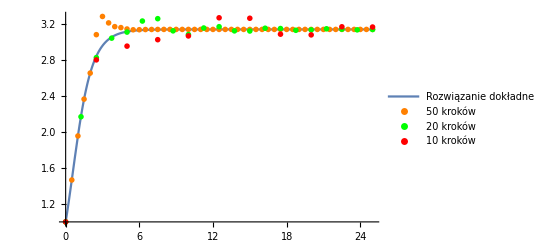

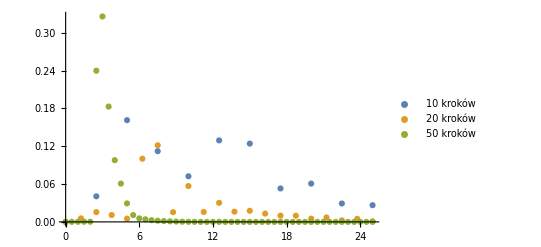

Największy błąd przy 10 krokach: 0.161417

Największy błąd przy 20 krokach: 0.121529

Największy błąd przy 50 krokach: 0.325934

Średni błąd przy 10 krokach: 0.0736053

Średni błąd przy 20 krokach: 0.022118

Średni błąd przy 50 krokach: 0.0189435

```mathematica
(* Rozwiązanie dokładne *)
result = DSolve[{yy'[x]==Sin[yy[x]], yy[0]==1}, yy[x],x];
res = result⟦1,1,2⟧;
resPoints = Table[res/.{x->i}, {i, 0,25,.1}];
resultPlot = Plot[res, {x,0,25}, PlotRange->All, PlotLegends->LineLegend[{"Rozwiązanie dokładne"}]];
(* Rozwiązania metodą Adamsa-Moultona *)
mamRes10 = mam[func, 0,1, 25, 10, 5];
mamRes20 = mam[func, 0,1, 25, 20, 5];
mamRes50 = mam[func, 0,1, 25, 50, 5];
mamRes10Plot = ListPlot[mamRes10,PlotStyle->{PointSize[.01],Red}, PlotLegends->LineLegend[{"10 kroków"}]];
mamRes20Plot = ListPlot[mamRes20,PlotStyle->{PointSize[.01],Green}, PlotLegends->LineLegend[{"20 kroków"}]];
mamRes50Plot = ListPlot[mamRes50,PlotStyle->{PointSize[.01],Orange}, PlotLegends->LineLegend[{"50 kroków"}]];
Show[resultPlot,mamRes50Plot, mamRes20Plot, mamRes10Plot, PlotRange->All]
(* Błędy *)
error10 = Table[{mamRes10⟦i,1⟧, Abs[(res/.x->mamRes10⟦i,1⟧)-mamRes10⟦i,2⟧]},{i, 1, Length[mamRes10]}];
error20 = Table[{mamRes20⟦i,1⟧, Abs[(res/.x->mamRes20⟦i,1⟧)-mamRes20⟦i,2⟧]},{i, 1, Length[mamRes20]}];
error50 = Table[{mamRes50⟦i,1⟧, Abs[(res/.x->mamRes50⟦i,1⟧)-mamRes50⟦i,2⟧]},{i, 1, Length[mamRes50]}];
ListPlot[{error10, error20, error50},  PlotLegends->{LineLegend[{"10 kroków", "20 kroków", "50 kroków"}]},
PlotRange->All]
Print["Największy błąd przy 10 krokach: ",  FindMaxError[error10]];
Print["Największy błąd przy 20 krokach: ",  FindMaxError[error20]];
Print["Największy błąd przy 50 krokach: ",  FindMaxError[error50]];
Print["Średni błąd przy 10 krokach: ",  FindAvgError[error10]];
Print["Średni błąd przy 20 krokach: ",  FindAvgError[error20]];
Print["Średni błąd przy 50 krokach: ",  FindAvgError[error50]];
```